# Stian’s Mathematica package – Miscellaneous functions

## Setup

Export usage messages

```mathematica
Begin["`Private`"];

packagename=FileNameTake@NotebookDirectory[];
sectionname=First@Flatten@StringCases[NotebookImport[NotebookFileName[],"Title"],"\\[Dash] "~~x:LetterCharacter..:>x];

<<Stians`;

messagefile=FileNameJoin[{
NotebookDirectory[],
"Messages",
packagename<>sectionname<>".txt"
}];

functions=NotebookImport[NotebookFileName[],"Subchapter"][[3;;]];

notebooks=FileNameJoin[{
NotebookDirectory[],
"Documentation",
"English",
"ReferencePages",
"Symbols",
#<>".nb"}]&/@functions;

found=Select[notebooks,FileExistsQ];

If[Complement[notebooks,found]≠{},
Print["Missing documentation pages:"];Print[Column[FileNameTake/@Complement[notebooks,found]]]];


NeatUsage[#,messagefile]&/@found;
```

Missing documentation pages:

ColourTriad.nb
ComplementaryColour.nb
GradeCalculation.nb
LaTeXReminderCheck.nb
PlagiarismCheck.nb
PokémonTeamTest.nb

Start package

```mathematica
(* 1. Automatically detected package- and section names *)
```

```mathematica
Print[packagename<>"`"<>sectionname<>"`"]
```

Stians`Miscellaneous`

```mathematica
(* 2. Automatically suggested file with usage messages *)
```

```mathematica
"<< "<>packagename<>"/Messages/"<>FileNameTake@messagefile
```

<< Stians/Messages/StiansMiscellaneous.txt

```mathematica
(* End of preamble *)
```

```mathematica
End[];
```

```mathematica
BeginPackage["Stians`Miscellaneous`"];
```

```mathematica
(* Import usage messages from file *)
```

```mathematica
<< "Stians/Messages/StiansMiscellaneous.txt"
```

## Definitions

PolygonArea

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Begin["`Private`"];
```

```mathematica
PolygonArea[input_List]:=Module[{n,i,s,dets},
n=Length[input];
For[i=1;s=0,
i<Length[input],
i++,
s=s+Det[{input[[i]],input[[i+1]]}]];
dets=s+Det[{input[[n]],input[[1]]}];
Abs[dets/2]
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

```mathematica
PolygonArea[{{1,2},{5/2,4},{4,3},{3,-2}}]
```

37/4

ColourConversion

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Colour::invRGB="RGB colours should be a list of three integers.";
Colour::invHTMLlength="HTML colours should be six characters long.";
Colour::invHTML="HTML colours should only contain digits or letters a–e.";
Colour::inv="Invalid input.";
```

```mathematica
Begin["`Private`"];
```

```mathematica
ColourConversion[{R_Integer,G_Integer,B_Integer}]:=Module[{r,g,b,temp1,temp2,temp3,i},
r=IntegerString[R,16];
g=IntegerString[G,16];
b=IntegerString[B,16];
temp1={r,g,b};
temp2={};
For[i=1,i<4,i++,
If[StringLength[Part[temp1,i]]==1,
AppendTo[temp2,StringJoin["0",Part[temp1,i]]],
AppendTo[temp2,Part[temp1,i]]]];
temp3=StringJoin@temp2;
temp3
]
```

```mathematica
ColourConversion[HTML_]:=Module[{html,r,g,b,R,G,B},
html=ToString[HTML];
r=StringTake[html,{1,2}];
g=StringTake[html,{3,4}];
b=StringTake[html,{5,6}];
R=FromDigits[r,16];
G=FromDigits[g,16];
B=FromDigits[b,16];
{R,G,B}
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

```mathematica
ColourConverson[{0,175,200}]
```

ColourConverson[{0,175,200}]

```mathematica
ColourConverson[{123,0,85}]
```

ColourConverson[{123,0,85}]

```mathematica
ColourConverson["0e120a"]
```

ColourConverson[0e120a]

ComplementaryColour

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Begin["`Private`"];
```

```mathematica
ComplementaryColour[input_]:=Module[{type,c,c1,c2,m1,m2,m3,colour},
(* Interpreting and testing input format *)
	If[!AnyTrue[Head[input]===#&/@{String,List},TrueQ],Message[Colour::inv];Abort[]];

	(* RGB input *)
		If[Head[input]==List,
		If[!Length@Flatten[input]==3,Message[Colour::invRGB];Abort[]];
		c=input;
		type="RGB"];

	(* HTML input *)
		If[Head[input]==String,
		If[!StringLength[input]==6,Message[Colour::invHTMLlength];Abort[]];
		If[!StringLength[StringReplace[input,{DigitCharacter,"a","b","c","d","e","f"}->""]]==0,Message[Colour::invHTML];Abort[]];
		c=ColourConversion[input];
		type="HTML"];


(* Step A: If at least two values are identical, swap them *)
	If[!DuplicateFreeQ[c],
	{c1,c2}=DeleteDuplicates[c][[{1,-1}]];
	colour=c/.{c1->c2,c2->c1}];

(* Step B: If all values are distinct, first swap position of the minimum and maximum values *)
(* The remaining middle position will be filled by 'max - middle + min' *)
	If[DuplicateFreeQ[c],
	{m1,m2,m3}={Min[c],Max[c],Sort[c][[2]]};
	colour=c/.{m1->m2,m2->m1,m3->m2-m3+m1}];

Which[
	type=="RGB",colour,
	type=="HTML",ColourConversion[colour]]
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

```mathematica
ComplementaryColour[{140,27,240}]
```

{127,240,27}

```mathematica
ComplementaryColour["0e5c40"]
```

5c0e2a

```mathematica
ComplementaryColour[{14,92,64}]
```

{92,14,42}

```mathematica
ComplementaryColour[{200,90,0}]
```

{0,110,200}

ColourTriad

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Options[ColourTriad]={"Display"->False,"Format"->Null};
```

```mathematica
Begin["`Private`"];
```

```mathematica
ColourTriad[input_,OptionsPattern@ColourTriad]:=Module[{type,c,p,colour,format,output,rgb},
(* Interpreting and testing input format *)
	If[!AnyTrue[Head[input]===#&/@{String,List},TrueQ],Message[Colour::inv];Abort[]];

	(* RGB input *)
		If[Head[input]==List,
		If[!Length@Flatten[input]==3,Message[Colour::invRGB];Abort[]];
		c=input;
		type="RGB"];

	(* HTML input *)
		If[Head[input]==String,
		If[!StringLength[input]==6,Message[Colour::invHTMLlength];Abort[]];
		If[!StringLength[StringReplace[input,{DigitCharacter,"a","b","c","d","e","f"}->""]]==0,Message[Colour::invHTML];Abort[]];
		c=ColourConversion[input];
		type="HTML"];

(* Cycle the values *)
	p=Select[Permutations[Range@3],Signature[#]==1&];
	colour={c[[#1]],c[[#2]],c[[#3]]}&@@p;

(* Option: Output format *)
	format=OptionValue["Format"];
	Which[
	format=="RGB"||format=="rgb",type="RGB",
	format=="HTML"||format=="html",type="HTML",
	True,Null];	

Which[
	type=="RGB",output=colour,
	type=="HTML",output=ColourConversion/@colour];

(* Option: Display colours *)
	If[OptionValue["Display"],
	rgb=RGBColor@@@(colour/255);
	Graphics[
	{
	{rgb[[1]],Rectangle[{0,0}]},
	{rgb[[2]],Rectangle[{1,0}]},
	{rgb[[3]],Rectangle[{2,0}]}
	}
	],
	output]
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

```mathematica
ColourTriad[{12,140,71}]
```

{{12,140,71},{140,71,12},{71,12,140}}

```mathematica
ColourConversion["0c8c47"]
```

{12,140,71}

```mathematica
ColourConversion[{12,140,71}]
```

0c8c47

```mathematica
ColourTriad["0c8c47"]
```

{0c8c47,8c470c,470c8c}

### Display

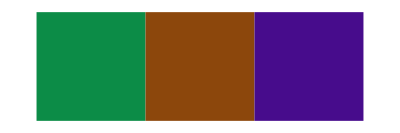

```mathematica
ColourTriad[{12,140,71},"Display"->True]
```

```mathematica
ColourTriad["0c8c47","Display"->True]
```

-Graphics-

LaTeXReminderCheck

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
LaTeXReminderCheck::ok="No duplicates found.";
LaTeXReminderCheck::dup="`1` duplicates were found.";
```

```mathematica
Begin["`Private`"];
```

```mathematica
LaTeXReminderCheck[file_String:
"/Users/Stian/Dropbox/Prosjekter/LaTeX/Guider og hjelp/LaTeX reminders.txt"
]:=Module[{temp1,a,b,temp2,temp3,temp4,temp5},

temp1=Import[file,"Data"];

{a,b}=Position[temp1,#][[1,1]]&/@{"Custom shortcuts in TexitEasy:","Custom shortcuts in Texmaker:"};

temp2=StringCases[ToString/@temp1[[a;;b]],{WordCharacter,"[","]"}..~~Repeated[" + "~~{WordCharacter..,_}]]/.{}->Nothing;

temp3=Gather[ToString/@temp2];

If[Evaluate[(Length/@temp3)/.{1->Nothing}]=={},Message[LaTeXReminderCheck::ok];Goto["End"]];

temp4=DeleteDuplicates@Flatten@Select[temp3,Length[#]==2&];

temp5=StringDelete[temp4,{"{","}"}];

Message[LaTeXReminderCheck::dup,Length@temp5];Print@TableForm@temp5;


Label["End"];
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

```mathematica
LaTeXReminderCheck[]
```

LaTeXReminderCheck::dup: 7 duplicates were found.

cmd + B
cmd + shift + E
cmd + I
cmd + shift + I
cmd + F
ctrl + .
ctrl + ,

PlagiarismCheck

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Begin["`Private`"];
```

```mathematica
PlagiarismCheck[input_String]:=Module[{temp,temp2,temp3,temp4},
temp=FileNameJoin[
{$TemporaryDirectory,ToString@Unique["temp"]<>".pdf"}];
CopyFile[input,temp];

temp2=ChangeExtension[temp,"txt"];
temp3=Import[temp2,"String"];
temp4=Hash[temp3,"MD5"];
IntegerString[temp4,16]
]
```

```mathematica
PlagiarismCheck[input_List]:=Module[{list,found,n,h,i},
list=<||>;
found={};

Do[
n=input[[i]];
h=PlagiarismCheck@input[[i]];
If[KeyExistsQ[list,h],
AppendTo[found,{list[h],n}]];
AppendTo[list,h->n],
{i,Length@input}];

found
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

```mathematica
PlagiarismCheck["/Users/Stian/Desktop/test.pdf"]
```

2c7948bb403bef34624ebe162e6ba50f

```mathematica
pdfs=FileNames["*.pdf","/Users/Stian/Downloads/Øving 9  Teori-innlevering 2_1094895",Infinity];
PlagiarismCheck@pdfs
```

PokémonTeamTest

## Development

```mathematica
T0=({{1, 1, 1, 1, 1, .5, 1, 0, .5, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {2, 1, .5, .5, 1, 2, .5, 0, 2, 1, 1, 1, 1, .5, 2, 1, 2, .5}, {1, 2, 1, 1, 1, .5, 2, 1, .5, 1, 1, 2, .5, 1, 1, 1, 1, 1}, {1, 1, 1, .5, .5, .5, 1, .5, 0, 1, 1, 2, 1, 1, 1, 1, 1, 2}, {1, 1, 0, 2, 1, 2, .5, 1, 2, 2, 1, .5, 2, 1, 1, 1, 1, 1}, {1, .5, 2, 1, .5, 1, 2, 1, .5, 2, 1, 1, 1, 1, 2, 1, 1, 1}, {1, .5, .5, .5, 1, 1, 1, .5, .5, .5, 1, 2, 1, 2, 1, 1, 2, .5}, {0, 1, 1, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 2, 1, 1, .5, 1}, {1, 1, 1, 1, 1, 2, 1, 1, .5, .5, .5, 1, .5, 1, 2, 1, 1, 2}, {1, 1, 1, 1, 1, .5, 2, 1, 2, .5, .5, 2, 1, 1, 2, .5, 1, 1}, {1, 1, 1, 1, 2, 2, 1, 1, 1, 2, .5, .5, 1, 1, 1, .5, 1, 1}, {1, 1, .5, .5, 2, 2, .5, 1, .5, .5, 2, .5, 1, 1, 1, .5, 1, 1}, {1, 1, 2, 1, 0, 1, 1, 1, 1, 1, 2, .5, .5, 1, 1, .5, 1, 1}, {1, 2, 1, 2, 1, 1, 1, 1, .5, 1, 1, 1, 1, .5, 1, 1, 0, 1}, {1, 1, 2, 1, 2, 1, 1, 1, .5, .5, .5, 2, 1, 1, .5, 2, 1, 1}, {1, 1, 1, 1, 1, 1, 1, 1, .5, 1, 1, 1, 1, 1, 1, 2, 1, 0}, {1, .5, 1, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 2, 1, 1, .5, .5}, {1, 2, 1, .5, 1, 1, 1, 1, .5, .5, 1, 1, 1, 1, 1, 2, 2, 1}});
```

```mathematica
T=({{Null,"normal","fight","flying","poison","ground","rock","bug","ghost","steel","fire","water","grass","electric","psychic","ice","dragon","dark","fairy"},{"normal",1,1,1,1,1,.5,1,0,.5,1,1,1,1,1,1,1,1,1},{"fight",2,1,.5,.5,1,2,.5,0,2,1,1,1,1,.5,2,1,2,.5},{"flying",1,2,1,1,1,.5,2,1,.5,1,1,2,.5,1,1,1,1,1},{"poison",1,1,1,.5,.5,.5,1,.5,0,1,1,2,1,1,1,1,1,2},{"ground",1,1,0,2,1,2,.5,1,2,2,1,.5,2,1,1,1,1,1},{"rock",1,.5,2,1,.5,1,2,1,.5,2,1,1,1,1,2,1,1,1},{"bug",1,.5,.5,.5,1,1,1,.5,.5,.5,1,2,1,2,1,1,2,.5},{"ghost",0,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,.5,1},{"steel",1,1,1,1,1,2,1,1,.5,.5,.5,1,.5,1,2,1,1,2},{"fire",1,1,1,1,1,.5,2,1,2,.5,.5,2,1,1,2,.5,1,1},{"water",1,1,1,1,2,2,1,1,1,2,.5,.5,1,1,1,.5,1,1},{"grass",1,1,.5,.5,2,2,.5,1,.5,.5,2,.5,1,1,1,.5,1,1},{"electric",1,1,2,1,0,1,1,1,1,1,2,.5,.5,1,1,.5,1,1},{"psychic",1,2,1,2,1,1,1,1,.5,1,1,1,1,.5,1,1,0,1},{"ice",1,1,2,1,2,1,1,1,.5,.5,.5,2,1,1,.5,2,1,1},{"dragon",1,1,1,1,1,1,1,1,.5,1,1,1,1,1,1,2,1,0},{"dark",1,.5,1,1,1,1,1,2,1,1,1,1,1,2,1,1,.5,.5},{"fairy",1,2,1,.5,1,1,1,1,.5,.5,1,1,1,1,1,2,2,1}});
```

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Default[PokemonTeamTest,2]=({{Null,"normal","fight","flying","poison","ground","rock","bug","ghost","steel","fire","water","grass","electric","psychic","ice","dragon","dark","fairy"},{"normal",1,1,1,1,1,.5,1,0,.5,1,1,1,1,1,1,1,1,1},{"fight",2,1,.5,.5,1,2,.5,0,2,1,1,1,1,.5,2,1,2,.5},{"flying",1,2,1,1,1,.5,2,1,.5,1,1,2,.5,1,1,1,1,1},{"poison",1,1,1,.5,.5,.5,1,.5,0,1,1,2,1,1,1,1,1,2},{"ground",1,1,0,2,1,2,.5,1,2,2,1,.5,2,1,1,1,1,1},{"rock",1,.5,2,1,.5,1,2,1,.5,2,1,1,1,1,2,1,1,1},{"bug",1,.5,.5,.5,1,1,1,.5,.5,.5,1,2,1,2,1,1,2,.5},{"ghost",0,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,.5,1},{"steel",1,1,1,1,1,2,1,1,.5,.5,.5,1,.5,1,2,1,1,2},{"fire",1,1,1,1,1,.5,2,1,2,.5,.5,2,1,1,2,.5,1,1},{"water",1,1,1,1,2,2,1,1,1,2,.5,.5,1,1,1,.5,1,1},{"grass",1,1,.5,.5,2,2,.5,1,.5,.5,2,.5,1,1,1,.5,1,1},{"electric",1,1,2,1,0,1,1,1,1,1,2,.5,.5,1,1,.5,1,1},{"psychic",1,2,1,2,1,1,1,1,.5,1,1,1,1,.5,1,1,0,1},{"ice",1,1,2,1,2,1,1,1,.5,.5,.5,2,1,1,.5,2,1,1},{"dragon",1,1,1,1,1,1,1,1,.5,1,1,1,1,1,1,2,1,0},{"dark",1,.5,1,1,1,1,1,2,1,1,1,1,1,2,1,1,.5,.5},{"fairy",1,2,1,.5,1,1,1,1,.5,.5,1,1,1,1,1,2,2,1}});

PokemonTeamTest::InvType="«`1`» is not a valid Pokémon type.";
PokemonTeamTest::InvTypes="«`1`» are not a valid Pokémon types.";
PokemonTeamTest::NotString="Pokémon types must be strings.";
PokemonTeamTest::OK="Pokémon team OK.";
```

```mathematica
Begin["`Private`"];
```

```mathematica
PokemonTeamTest[pokemon_,typetable_.]:=Module[
{alltypes,notpokemon,ttable,pkmn,str,goodagainst,good,missing},
(* Basic information *)
	alltypes=typetable[[1,2;;]];
	notpokemon=Complement[pokemon,alltypes];

(* Input check *)
	If[notpokemon≠{},
	If[Length[notpokemon]==1,
	Message[PokemonTeamTest::InvType,First@notpokemon];Abort[],
	Message[PokemonTeamTest::InvTypes,notpokemon]
	]];

	If[!AllTrue[pokemon,StringQ],Message[PokemonTeamTest::NotString];Abort[]];

(* Keeping rows with given types *)
	ttable=typetable[[2;;]];
	pkmn=Select[ttable,MemberQ[pokemon,First[#]]&];

(* Finding which types the team is effective against *)
	str=Last/@Position[pkmn,2];
	goodagainst=typetable[[1,#]]&/@str;
	good=DeleteDuplicates@goodagainst;

(* Missing types effective against... *)
	missing=Complement[alltypes,good];

(* Returning result *)
	If[missing=={},Message[PokemonTeamTest::OK],Return@missing];
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

Team A

Magnezone
Pangoro
Whiscash
Dragonite
Gengar

```mathematica
PokemonTeamTest[{"electric","steel","fight","dark","water","ground","dragon","flying","ghost","poison"}]
```

PokemonTeamTest::OK: Pokémon team OK.

Team B

Litwick
Flygon
Magnezone
Whiscash
Pangoro
Dragonite

```mathematica
PokemonTeamTest[{"ghost","fire","ground","dragon","steel","electric","ground","water","dark","fight","dragon","flying"}]
```

PokemonTeamTest::OK: Pokémon team OK.

Team C – Pokémon Omega Ruby
Breloom	grass	fight		poison heal	460	pokeball
Flygon		ground	dragon		levitate		520	premiere ball
Whiscash	water	ground		oblivious	468	dive ball
Magnezone	electric	steel		magnet pull	535	ultra ball
Spiritomb	ghost	dark		pressure	485	luxury ball
Skarmory	steel	flying		keen eye	465	great ball

```mathematica
PokemonTeamTest[{"grass","fight","ground","dragon","water","electric","steel","ghost","dark","flying","ice"}]
```

PokemonTeamTest::OK: Pokémon team OK.

Team D – Pokémon Omega Ruby team II
Breloom	grass	fight		poison heal	460	pokeball
Flygon		ground	dragon		levitate		520	premiere ball
Alakazam	psychic		synchronize	500	quick ball
Magnezone	electric	steel		magnet pull	535	ultra ball
Chandelure	ghost	fire		flame body	520	luxury ball
Whiscash	water	ground		oblivious	468	dive ball

```mathematica
PokemonTeamTest[{"grass","fight","ground","dragon","psychic","electric","steel","fire","ghost"}]
```

PokemonTeamTest::OK: Pokémon team OK.

```mathematica
PokemonTeamTest[{"grass","fight","ground","dragon","psychic","electric","steel","fire","ghost","water","ground"}]
```

PokemonTeamTest::OK: Pokémon team OK.

Team E – Pokémon Omega Ruby team III

```mathematica
{{Chandelure, female, ghost, fire, □, 520, luxury ball, □, □, □, □}, {Wigglytuff, female, normal, fairy, cute charm, 425, heal ball, dazzlin gleam, sweet kiss, hyper beam, blizzard}, {Gardevoir, female, psychic, fairy, trace, 518, □, hypnosis, dream eater, moonblast, stored power}, {Empoleon, male, water, steel, □, 530, □, hydro pump, flash cannon, surf, □}, {Breloom, male, grass, fight, poison heal, 460, pokeball, □, □, □, □}, {Flygon, female, ground, dragon, levitate, 520, premiere ball, □, □, □, □}}
```

```mathematica
PokemonTeamTest[{"ghost","fire","normal","fairy","psychic","water","steel","grass","fight","ground","dragon"}]
```

{flying}

GradeCalculation

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
GradeCalculation::invalid="Invalid input.";
```

```mathematica
Begin["`Private`"];
```

```mathematica
GradeCalculation[input__]:=(
(* Gather numbers in a list *)
	GradeCalculation[{input}]
)
```

```mathematica
GradeCalculation[input_]:=Module[{L,Letter,Number,sum,averagegrade},
(* Input check *)
	L=Length[input];
	If[!MemberQ[{5,6},L],Message[GradeCalculation::invalid];Abort[]];

(* Conversion functions *)
	Letter[number_]:=Which[
	number<0.5,           "F",
	0.5≤number<1.5,"E",
	1.5≤number<2.5,"D",
	2.5≤number<3.5,"C",
	3.5≤number<4.5,"B",
	number≥4.5,           "A"];

	Number[letter_]:=Which[
	letter=="F",0,
	letter=="E",1,
	letter=="D",2,
	letter=="C",3,
	letter=="B",4,
	letter=="A",5,
	NumericQ[letter],letter];

(* Average grade of an exam *)
	Which[
	L==5,sum=input.(Number/@{"A","B","C","D","E"}),
	L==6,sum=input.(Number/@{"A","B","C","D","E","F"})];
	
averagegrade=Letter[sum/Total@input]
]
```

```mathematica
GradeCalculation[input_?MatrixQ]:=Module[{Letter,Number,grades,weights,gpa},
(* Conversion functions *)
	Letter[number_]:=Which[
	number<0.5,           "F",
	0.5≤number<1.5,"E",
	1.5≤number<2.5,"D",
	2.5≤number<3.5,"C",
	3.5≤number<4.5,"B",
	number≥4.5,           "A"];

	Number[letter_]:=Which[
	letter=="F",0,
	letter=="E",1,
	letter=="D",2,
	letter=="C",3,
	letter=="B",4,
	letter=="A",5,
	NumericQ[letter],letter];

(* Grade point average *)
	grades=Number/@input[[All,1]];
	weights=input[[All,2]];
	gpa=(grades.weights)/Total[weights];

{NumberForm[N[gpa],3],Letter@gpa}
]
```

```mathematica
End[];
```

## Testing

### Basic demonstration

#### Average grade of an exam, not counting fails (UiS default)

```mathematica
GradeCalculation[12,7,2,0,0]
```

B

```mathematica
GradeCalculation[12,7,2,0,0]
```

B

```mathematica
GradeCalculation[19,17,18,8,8]
```

C

#### Average grade of an exam, counting fails

```mathematica
GradeCalculation[54,41,66,24,12,80]
```

D

### Grade point average (GPA) calculations

#### First quarter at GRCC

```mathematica
GradeCalculation[{
{4.0,5.0},{3.9,2.0},{4.0,5.0},{3.8,5.0},{4.0,1.0}
}]
```

{3.93,B}

#### Bachelor at UiS

```mathematica
GradeCalculation[{
{"C",5},{"A",15},{"B",10},{"A",5},{"A",10},{"B",10},{"A",5},{"A",5},{"B",5},{"A",10},{"B",10},{"A",5},{"B",10},{"A",10},{"A",5},{"A",5},{"B",10},{"A",10},{"A",5},{"A",10},{"B",10},{"C",10}
}]
```

{4.47,B}

#### Master at UiS

```mathematica
GradeCalculation[({{"C", 10}, {"B", 10}, {"A", 10}, {"A", 10}, {"B", 10}, {"B", 10}})]
```

{4.17,B}

### Wrong usage

```mathematica
GradeCalculation[1,2,3]
```

GradeCalculation::invalid: Invalid input.

$Aborted

GridToLaTeX

## Development

#### Table dimensions

```mathematica
<<Xray`
```

```mathematica
tab=StructureFactorTable[0.70913713,"silicon","mOverBar[3]m",{h_,k_,l_}/;OddQ[h]||Divisible[h+k+l,4],
"Sort"->3,"Keep"->9]
```

| Structure factor | Phase | Bragg angle | Pendellösung distance | Darwin width
(hkl) | F_hkl | ϕ_hkl [°] | θ_B [°] | Λ_0 [µm] | 2δ_os [µrad]
(111) | 59.374 | -179.620 | 6.493 | 42.140 | 14.881
(220) | 68.225 | -179.540 | 10.641 | 36.275 | 10.586
(311) | 44.716 | -179.510 | 12.506 | 54.979 | 5.957
(400) | 57.093 | -179.470 | 15.138 | 42.576 | 6.378
(533) | 25.639 | -179.250 | 25.348 | 88.762 | 1.866
(444) | 33.581 | -179.200 | 26.893 | 66.878 | 2.344
(551) | 22.700 | -179.180 | 27.791 | 98.139 | 1.550
(642) | 29.830 | -179.130 | 29.246 | 73.658 | 1.971
(553) | 20.203 | -179.100 | 30.098 | 107.840 | 1.311

```mathematica
tab[[1]]
```

{{Null,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width},{(hkl),F_hkl,ϕ_hkl [°],θ_B [°],Λ_0 [µm],2δ_os [µrad]},{(111),59.374,-179.620,6.493,42.140,14.881},{(220),68.225,-179.540,10.641,36.275,10.586},{(311),44.716,-179.510,12.506,54.979,5.957},{(400),57.093,-179.470,15.138,42.576,6.378},{(533),25.639,-179.250,25.348,88.762,1.866},{(444),33.581,-179.200,26.893,66.878,2.344},{(551),22.700,-179.180,27.791,98.139,1.550},{(642),29.830,-179.130,29.246,73.658,1.971},{(553),20.203,-179.100,30.098,107.840,1.311}}

```mathematica
Head@tab
```

Grid

```mathematica
Length@tab
```

6

```mathematica
Length@tab[[1]]
```

11

```mathematica
dim={Length@First[#],Length[#]}&[tab]
```

{11,6}

Non-formatted table:

```mathematica
tab2=Grid@{{1211,-1,-2,5,233.45,65},{1214,-1,-2,5,233.85,145},{1225,-1,-2,5,234.35,302},{1230,-1,-2,5,235.25,652},{1232,-1,-2,5,235.85,941},{1236,-1,-2,5,236.45,2648},{1241,-1,-2,5,236.95,3772},{1242,-1,-2,5,237.25,4269},{1249,-1,-2,5,237.75,2525},{1256,-1,-2,5,238.45,669},{1259,-1,-2,5,238.95,495},{1266,-1,-2,5,240.45,161},{1270,-1,-2,5,241.45,99},{1275,-1,-2,5,242.25,95},{1279,-1,-2,5,242.95,93},{1281,-1,-2,5,243.25,84},{1285,-1,-2,5,243.55,90},{1288,-1,-2,5,243.85,82},{1291,-1,-2,5,244.25,95},{1295,-1,-2,5,244.65,86},{1302,-1,-2,5,245.45,120},{1304,-1,-2,5,247.25,219},{1316,-1,-2,5,248.75,1549},{1326,-1,-2,5,248.75,1549},{1329,-1,-2,5,249.25,3822},{1332,-1,-2,5,249.55,4029},{1337,-1,-2,5,250.15,3162},{1341,-1,-2,5,250.95,1420},{1344,-1,-2,5,251.45,935},{1349,-1,-2,5,252.15,424},{1352,-1,-2,5,252.85,166},{1356,-1,-2,5,253.55,97},{1357,-1,-2,5,253.75,59}};
```

```mathematica
Length@tab2
```

1

```mathematica
If[Length@tab>1,
(* Formatted table *)dim={Length@First[#],Length@First@First[#]}&[tab],
(* Non-formatted table *)dim=Dimensions@First@tab]
```

{20,11}

#### Table content

```mathematica
cont=ToString[#,StandardForm]&/@Flatten@First@tab
```

{Null,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width,(hkl),F_hkl,ϕ_hkl [°],θ_B [°],Λ_0 [µm],2δ_os [µrad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

The following has a FullForm that is easier to handle:

```mathematica
cont=ToString/@Flatten@First@tab
```

{Null,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width,(hkl),F
 hkl,ϕ    [°]
 hkl,θ  [°]
 B,Λ  [µm]
 0,2δ   [µrad]
  os,(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

```mathematica
(*temp=Riffle[cont,{"&"}]*)
```

```mathematica
temp=Partition[temp,dim[[1]]]
```

{{,Structure factor,Phase,Bragg angle,Pendell\[ODoubleDot]sung distance,Darwin width,(hkl),${F}_{hkl}$,${\phi}_{hkl}$ [\si{\degree}],${\theta}_{B}$ [\si{\degree}],${\Lambda}_{0}$ [$\mu$ m]},{${2\delta}_{os}$ [$\mu$ rad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641},{36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470},{15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581},{-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642)},{29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}}

#### Correct empty cells

```mathematica
temp=cont/."Null"->""
```

{,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width,(hkl),F
 hkl,ϕ    [°]
 hkl,θ  [°]
 B,Λ  [µm]
 0,2δ   [µrad]
  os,(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

#### Correct subscripts

```mathematica
FullForm@temp[[9]]
```

"\[Phi]    [\[Degree]]
 hkl"

```mathematica
FullForm@temp[[11]]
```

"\[CapitalLambda]  [\[Micro]m]
 0"

```mathematica
temp=StringReplace[temp,
{pre:Except[" "]..~~"\n"~~sub__:>
"{"<>pre<>"}"<>"_{"<>StringTrim@sub<>"}",
pre1:Except[" "]..~~" "..|"\\n"~~pre2___~~"\n"~~sub__:>
"{"<>pre1<>"}"<>"_{"<>StringTrim@sub<>"} "<>pre2}]
```

{,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width,(hkl),{F}_{hkl},{ϕ}_{hkl} [°],{θ}_{B} [°],{Λ}_{0} [µm],{2δ}_{os} [µrad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

```mathematica
temp[[13;;23;;2]]//TableForm
```

(111)
-179.620
42.140
(220)
-179.540
36.275

#### Correct greek letters

```mathematica
greek={
{"alpha","beta","gamma","delta","epsilon","zeta","eta","theta","iota","kappa","lambda","mu","nu","xi","omicron","pi","rho","sigma","tau","upsilon","phi","chi","psi","omega"},
{"Alpha","Beta","Gamma","Delta","Epsilon","Zeta","Eta","Theta","Iota","Kappa","Lambda","Mu","Nu","Xi","Omicron","Pi","Rho","Sigma","Tau","Upsilon","Phi","Chi","Psi","Omega"},
{"CapitalAlpha","CapitalBeta","CapitalGamma","CapitalDelta","CapitalEpsilon","CapitalZeta","CapitalEta","CapitalTheta","CapitalIota","CapitalKappa","CapitalLambda","CapitalMu","CapitalNu","CapitalXi","CapitalOmicron","CapitalPi","CapitalRho","CapitalSigma","CapitalTau","CapitalUpsilon","CapitalPhi","CapitalChi","CapitalPsi","CapitalOmega"}};
```

```mathematica
rule1=Thread[greek[[3]]->greek[[2]]];
rule1="\\["<>#[[1]]<>"]"->"\\"<>#[[2]]&/@rule1;
```

```mathematica
rule2=Thread[greek[[2]]->greek[[1]]];
rule2="\\["<>#[[1]]<>"]"->"\\"<>#[[2]]&/@rule2;
```

```mathematica
extrarules={
"\\[Micro]"->"\\mu",
"\\[Degree]"->"\\si{\\degree}"};
```

```mathematica
rules=Join@@{rule1,rule2,extrarules}
```

{\[CapitalAlpha]→\Alpha,\[CapitalBeta]→\Beta,\[CapitalGamma]→\Gamma,\[CapitalDelta]→\Delta,\[CapitalEpsilon]→\Epsilon,\[CapitalZeta]→\Zeta,\[CapitalEta]→\Eta,\[CapitalTheta]→\Theta,\[CapitalIota]→\Iota,\[CapitalKappa]→\Kappa,\[CapitalLambda]→\Lambda,\[CapitalMu]→\Mu,\[CapitalNu]→\Nu,\[CapitalXi]→\Xi,\[CapitalOmicron]→\Omicron,\[CapitalPi]→\Pi,\[CapitalRho]→\Rho,\[CapitalSigma]→\Sigma,\[CapitalTau]→\Tau,\[CapitalUpsilon]→\Upsilon,\[CapitalPhi]→\Phi,\[CapitalChi]→\Chi,\[CapitalPsi]→\Psi,\[CapitalOmega]→\Omega,\[Alpha]→\alpha,\[Beta]→\beta,\[Gamma]→\gamma,\[Delta]→\delta,\[Epsilon]→\epsilon,\[Zeta]→\zeta,\[Eta]→\eta,\[Theta]→\theta,\[Iota]→\iota,\[Kappa]→\kappa,\[Lambda]→\lambda,\[Mu]→\mu,\[Nu]→\nu,\[Xi]→\xi,\[Omicron]→\omicron,\[Pi]→\pi,\[Rho]→\rho,\[Sigma]→\sigma,\[Tau]→\tau,\[Upsilon]→\upsilon,\[Phi]→\phi,\[Chi]→\chi,\[Psi]→\psi,\[Omega]→\omega,\[Micro]→\mu,\[Degree]→\si{\degree}}

```mathematica
temp=ToString/@FullForm/@temp
```

{"","Structure factor","Phase","Bragg angle","Pendell\[ODoubleDot]sung distance","Darwin width","(hkl)","{F}_{hkl}","{\[Phi]}_{hkl} [\[Degree]]","{\[Theta]}_{B} [\[Degree]]","{\[CapitalLambda]}_{0} [\[Micro]m]","{2\[Delta]}_{os} [\[Micro]rad]","(111)","59.374","-179.620","6.493","42.140","14.881","(220)","68.225","-179.540","10.641","36.275","10.586","(311)","44.716","-179.510","12.506","54.979","5.957","(400)","57.093","-179.470","15.138","42.576","6.378","(533)","25.639","-179.250","25.348","88.762","1.866","(444)","33.581","-179.200","26.893","66.878","2.344","(551)","22.700","-179.180","27.791","98.139","1.550","(642)","29.830","-179.130","29.246","73.658","1.971","(553)","20.203","-179.100","30.098","107.840","1.311"}

```mathematica
temp=StringReplace[temp,{"\"\\\""~~c__~~"\\\"\"":>"\""<>c<>"\"","\""->""}]
```

{,Structure factor,Phase,Bragg angle,Pendell\[ODoubleDot]sung distance,Darwin width,(hkl),{F}_{hkl},{\[Phi]}_{hkl} [\[Degree]],{\[Theta]}_{B} [\[Degree]],{\[CapitalLambda]}_{0} [\[Micro]m],{2\[Delta]}_{os} [\[Micro]rad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

```mathematica
temp=StringReplace[temp,rules]
```

{,Structure factor,Phase,Bragg angle,Pendell\[ODoubleDot]sung distance,Darwin width,(hkl),{F}_{hkl},{\phi}_{hkl} [\si{\degree}],{\theta}_{B} [\si{\degree}],{\Lambda}_{0} [\mum],{2\delta}_{os} [\murad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

```mathematica
temp=StringReplace[temp,x:greek~~y:LetterCharacter..:>x<>" "<>y]
```

{,Structure factor,Phase,Bragg angle,Pendell\[ODoubleDot]sung distance,Darwin width,(hkl),{F}_{hkl},{\phi}_{hkl} [\si{\degree}],{\theta}_{B} [\si{\degree}],{\Lambda}_{0} [\mu m],{2\delta}_{os} [\mu rad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

Wrapping subscript expressions on the form {...}_{...} with $...$:

```mathematica
temp=StringReplace[temp,G:Shortest["{"~~__~~"}_{"~~__~~"}"]:>"$"<>G<>"$"]
```

{,Structure factor,Phase,Bragg angle,Pendell\[ODoubleDot]sung distance,Darwin width,(hkl),${F}_{hkl}$,${\phi}_{hkl}$ [\si{\degree}],${\theta}_{B}$ [\si{\degree}],${\Lambda}_{0}$ [\mu m],${2\delta}_{os}$ [\mu rad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

Finding unwrapped greek math:

```mathematica
temp=StringReplace[temp,
(q:(
p__/;(
StringMatchQ[p,"$"~~___~~"\\"~~greek~~___~~"$"]||
StringMatchQ[p,"\\"~~greek])
):>
StringReplace[q,{
Shortest["$"~~k__~~"$"]:>"§"~~k~~"§",
g:("\\"~~greek):>"$"<>g<>"$"}])/."§"->"$"
]
```

{,Structure factor,Phase,Bragg angle,Pendell\[ODoubleDot]sung distance,Darwin width,(hkl),${F}_{hkl}$,${\phi}_{hkl}$ [\si{\degree}],${\theta}_{B}$ [\si{\degree}],${\Lambda}_{0}$ [$\mu$ m],${2\delta}_{os}$ [$\mu$ rad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

```mathematica
(*temp=StringReplace[temp,G:("\\"~~greek~~Except[" "]..):>"$"<>G<>"$"]*)
```

#### Other corrections

```mathematica
extranonmath={
"\\[ODoubleDot]"->"ö"};
```

```mathematica
temp=StringReplace[temp,extranonmath]
```

{,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width,(hkl),${F}_{hkl}$, [\si{\degree}], [\si{\degree}], [$\mu$ m], [$\mu$ rad],(111),59.374,-179.620,6.493,42.140,14.881,(220),68.225,-179.540,10.641,36.275,10.586,(311),44.716,-179.510,12.506,54.979,5.957,(400),57.093,-179.470,15.138,42.576,6.378,(533),25.639,-179.250,25.348,88.762,1.866,(444),33.581,-179.200,26.893,66.878,2.344,(551),22.700,-179.180,27.791,98.139,1.550,(642),29.830,-179.130,29.246,73.658,1.971,(553),20.203,-179.100,30.098,107.840,1.311}

#### Writing out lines

```mathematica
tempfinal=Partition[temp,Last@dim]
```

{{,Structure factor,Phase,Bragg angle,Pendellösung distance,Darwin width},{(hkl),${F}_{hkl}$, [\si{\degree}], [\si{\degree}], [$\mu$ m], [$\mu$ rad]},{(111),59.374,-179.620,6.493,42.140,14.881},{(220),68.225,-179.540,10.641,36.275,10.586},{(311),44.716,-179.510,12.506,54.979,5.957},{(400),57.093,-179.470,15.138,42.576,6.378},{(533),25.639,-179.250,25.348,88.762,1.866},{(444),33.581,-179.200,26.893,66.878,2.344},{(551),22.700,-179.180,27.791,98.139,1.550},{(642),29.830,-179.130,29.246,73.658,1.971},{(553),20.203,-179.100,30.098,107.840,1.311}}

```mathematica
tempfinal=Riffle[#,{"&"}]&/@tempfinal
```

{{,&,Structure factor,&,Phase,&,Bragg angle,&,Pendellösung distance,&,Darwin width},{(hkl),&,${F}_{hkl}$,&, [\si{\degree}],&, [\si{\degree}],&, [$\mu$ m],&, [$\mu$ rad]},{(111),&,59.374,&,-179.620,&,6.493,&,42.140,&,14.881},{(220),&,68.225,&,-179.540,&,10.641,&,36.275,&,10.586},{(311),&,44.716,&,-179.510,&,12.506,&,54.979,&,5.957},{(400),&,57.093,&,-179.470,&,15.138,&,42.576,&,6.378},{(533),&,25.639,&,-179.250,&,25.348,&,88.762,&,1.866},{(444),&,33.581,&,-179.200,&,26.893,&,66.878,&,2.344},{(551),&,22.700,&,-179.180,&,27.791,&,98.139,&,1.550},{(642),&,29.830,&,-179.130,&,29.246,&,73.658,&,1.971},{(553),&,20.203,&,-179.100,&,30.098,&,107.840,&,1.311}}

```mathematica
tempfinal=StringJoin@Riffle[#," "]&/@tempfinal
```

{ & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width,(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad],(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881,(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586,(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957,(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378,(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866,(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344,(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550,(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971,(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311}

```mathematica
tempfinal=#<>" \\\\\n"&/@tempfinal
```

{ & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
,(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad] \\
,(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
,(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
,(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
,(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
,(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
,(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
,(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
,(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
,(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\
}

```mathematica
Print@@tempfinal
```

& Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad] \\
(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\

& Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
(hkl) & {F}_{hkl} & {$\phi}_{hkl}$ [\degree] & {$\theta}_{B}$ [\degree] & {$\Lambda}_{0}$ [\mu m] & {2$\delta}_{os}$ [\mu rad] \\
(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\

```mathematica
oo=Join@@{out,tempfinal}
```

{\begin{table}[]
,\centering
,\caption{My caption}
,\label{my-label}
,\begin{tabular}{llllll}
, & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
,(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad] \\
,(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
,(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
,(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
,(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
,(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
,(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
,(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
,(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
,(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\
}

```mathematica
out1={
"\\begin{tabular}{"<>StringJoin@ConstantArray["l",Last@dim]<>"}\n"
};

out2={
"\\end{tabular}"
};

Print@@Join@@
{{"\\begin{tabular}{"<>StringJoin@ConstantArray["l",Last@dim]<>"}\n"},
tempfinal,
{"\\end{tabular}"}};
```

\begin{tabular}{llllll}
 & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad] \\
(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\
\end{tabular}

```mathematica
(*Export["/Users/Stian/Desktop/test.txt",out,"Table"]*)
```

#### Feature – Wrap numbers, «\{…}»

```mathematica
tab1={" & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\\\\n","(hkl) & ${F}_{hkl}$ &  [\\si{\\degree}] &  [\\si{\\degree}] &  [$\\mu$ m] &  [$\\mu$ rad] \\\\\n","(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\\\\n","(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\\\\n","(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\\\\n","(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\\\\n","(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\\\\n","(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\\\\n","(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\\\\n","(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\\\\n","(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\\\\n"}
```

{ & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
,(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad] \\
,(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
,(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
,(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
,(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
,(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
,(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
,(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
,(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
,(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\
}

```mathematica
command="num";
```

```mathematica
StringReplace[tab1,t:{DigitCharacter,".","-"}..:>"\\"<>command<>"{"<>t<>"}"]
```

{ & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
,(hkl) & ${F}_{hkl}$ &  [\si{\degree}] &  [\si{\degree}] &  [$\mu$ m] &  [$\mu$ rad] \\
,(\num{111}) & \num{59.374} & \num{-179.620} & \num{6.493} & \num{42.140} & \num{14.881} \\
,(\num{220}) & \num{68.225} & \num{-179.540} & \num{10.641} & \num{36.275} & \num{10.586} \\
,(\num{311}) & \num{44.716} & \num{-179.510} & \num{12.506} & \num{54.979} & \num{5.957} \\
,(\num{400}) & \num{57.093} & \num{-179.470} & \num{15.138} & \num{42.576} & \num{6.378} \\
,(\num{533}) & \num{25.639} & \num{-179.250} & \num{25.348} & \num{88.762} & \num{1.866} \\
,(\num{444}) & \num{33.581} & \num{-179.200} & \num{26.893} & \num{66.878} & \num{2.344} \\
,(\num{551}) & \num{22.700} & \num{-179.180} & \num{27.791} & \num{98.139} & \num{1.550} \\
,(\num{642}) & \num{29.830} & \num{-179.130} & \num{29.246} & \num{73.658} & \num{1.971} \\
,(\num{553}) & \num{20.203} & \num{-179.100} & \num{30.098} & \num{107.840} & \num{1.311} \\
}

#### Problem with grid lines

```mathematica
If[Length@tab3>1,
dim={Length@First[#],Length[#]}&[tab3],
dim=Dimensions@First@tab3]
```

{20,4}

```mathematica
Length@tab3
```

4

## Definition

```mathematica
(* Messages and options *)
```

```mathematica
Options[GridToLaTeX]={"WrapNumbers"->False};
```

```mathematica
Begin["`Private`"];
```

```mathematica
GridToLaTeX[grid_Grid,OptionsPattern@GridToLaTeX]:=Module[{
dim,content,
greek,rule1,rule2,extrarules,rules,extranonmath,
temp
},

(* Table dimensions and content *)
	If[Length@grid>1,
	dim={Length@First[#],Length@First@First[#]}&[grid],
	dim=Dimensions@First@grid];
	content=ToString/@Flatten@First@grid;

(* Convert to string and correct empty cells *)
	temp=(ToString/@content)/."Null"->"";

(* Correct subscripts *)
	temp=StringReplace[temp,
	{pre:Except[" "]..~~"\n"~~sub__:>
	"{"<>pre<>"}"<>"_{"<>StringTrim@sub<>"}",
	pre1:Except[" "]..~~" "..|"\\n"~~pre2___~~"\n"~~sub__:>
	"{"<>pre1<>"}"<>"_{"<>StringTrim@sub<>"} "<>pre2}];

(* Correct greek *)
	greek={
{"alpha","beta","gamma","delta","epsilon","zeta","eta","theta","iota","kappa","lambda","mu","nu","xi","omicron","pi","rho","sigma","tau","upsilon","phi","chi","psi","omega"},
{"Alpha","Beta","Gamma","Delta","Epsilon","Zeta","Eta","Theta","Iota","Kappa","Lambda","Mu","Nu","Xi","Omicron","Pi","Rho","Sigma","Tau","Upsilon","Phi","Chi","Psi","Omega"},
{"CapitalAlpha","CapitalBeta","CapitalGamma","CapitalDelta","CapitalEpsilon","CapitalZeta","CapitalEta","CapitalTheta","CapitalIota","CapitalKappa","CapitalLambda","CapitalMu","CapitalNu","CapitalXi","CapitalOmicron","CapitalPi","CapitalRho","CapitalSigma","CapitalTau","CapitalUpsilon","CapitalPhi","CapitalChi","CapitalPsi","CapitalOmega"}};

	rule1=Thread[greek[[3]]->greek[[2]]];
	rule1="\\["<>#[[1]]<>"]"->"\\"<>#[[2]]&/@rule1;

	rule2=Thread[greek[[2]]->greek[[1]]];
	rule2="\\["<>#[[1]]<>"]"->"\\"<>#[[2]]&/@rule2;

	extrarules={
	"\\[Micro]"->"\\mu",
	"\\[Degree]"->"\\si{\\degree}"};

	rules=Join@@{rule1,rule2,extrarules};

	
	temp=ToString/@FullForm/@temp;

	(* Clearing extra quatiation marks *)
	temp=StringReplace[temp,{
	"\"\\\""~~c__~~"\\\"\"":>
	"\""<>c<>"\"","\""->""}];

	temp=StringReplace[temp,rules];

	temp=StringReplace[temp,x:greek~~y:LetterCharacter..:>x<>" "<>y];

	(* Wrapping subscript expressions on the form {...}_{...} with $...$ *)
	temp=StringReplace[temp,G:
	Shortest["{"~~__~~"}_{"~~__~~"}"]:>"$"<>G<>"$"];

	(* Finding unwrapped greek math *)
	temp=StringReplace[temp,
	(q:(
	p__/;(
	StringMatchQ[p,"$"~~___~~"\\"~~greek~~___~~"$"]||
	StringMatchQ[p,"\\"~~greek])
	):>
	StringReplace[q,{
	Shortest["$"~~k__~~"$"]:>"§"~~k~~"§",
	g:("\\"~~greek):>"$"<>g<>"$"}])/."§"->"$"
	];


(* Other corrections *)
	extranonmath={
	"\\[ODoubleDot]"->"ö",
	"_"->"\\textunderscore "};

	temp=StringReplace[temp,extranonmath];

(* Option: Wrap numbers *)
	If[StringQ@OptionValue["WrapNumbers"],
	temp=StringReplace[temp,t:{DigitCharacter,".","-"}..:>
	"\\"<>OptionValue["WrapNumbers"]<>"{"<>t<>"}"]];

(* Writing out lines *)
	temp=Partition[temp,Last@dim];
	temp=Riffle[#,{"&"}]&/@temp;
	temp=StringJoin@Riffle[#," "]&/@temp;
	temp=#<>" \\\\\n"&/@temp;

	Print@@Join@@
{{"\\begin{tabular}{"<>StringJoin@ConstantArray["c",Last@dim]<>"}\n"},
temp,
{"\\end{tabular}"}};	
]
```

```mathematica
End[];
```

## Testing

```mathematica
tab
```

| Structure factor | Phase | Bragg angle | Pendellösung distance | Darwin width
(hkl) | F_hkl | ϕ_hkl [°] | θ_B [°] | Λ_0 [µm] | 2δ_os [µrad]
(111) | 59.374 | -179.620 | 6.493 | 42.140 | 14.881
(220) | 68.225 | -179.540 | 10.641 | 36.275 | 10.586
(311) | 44.716 | -179.510 | 12.506 | 54.979 | 5.957
(400) | 57.093 | -179.470 | 15.138 | 42.576 | 6.378
(533) | 25.639 | -179.250 | 25.348 | 88.762 | 1.866
(444) | 33.581 | -179.200 | 26.893 | 66.878 | 2.344
(551) | 22.700 | -179.180 | 27.791 | 98.139 | 1.550
(642) | 29.830 | -179.130 | 29.246 | 73.658 | 1.971
(553) | 20.203 | -179.100 | 30.098 | 107.840 | 1.311

```mathematica
GridToLaTeX@tab
```

\begin{tabular}{cccccc}
 & Structure factor & Phase & Bragg angle & Pendellösung distance & Darwin width \\
(hkl) & ${F}_{hkl}$ & ${\phi}_{hkl}$ [\si{\degree}] & ${\theta}_{B}$ [\si{\degree}] & ${\Lambda}_{0}$ [$\mu$ m] & ${2\delta}_{os}$ [$\mu$ rad] \\
(111) & 59.374 & -179.620 & 6.493 & 42.140 & 14.881 \\
(220) & 68.225 & -179.540 & 10.641 & 36.275 & 10.586 \\
(311) & 44.716 & -179.510 & 12.506 & 54.979 & 5.957 \\
(400) & 57.093 & -179.470 & 15.138 & 42.576 & 6.378 \\
(533) & 25.639 & -179.250 & 25.348 & 88.762 & 1.866 \\
(444) & 33.581 & -179.200 & 26.893 & 66.878 & 2.344 \\
(551) & 22.700 & -179.180 & 27.791 & 98.139 & 1.550 \\
(642) & 29.830 & -179.130 & 29.246 & 73.658 & 1.971 \\
(553) & 20.203 & -179.100 & 30.098 & 107.840 & 1.311 \\
\end{tabular}

```mathematica
GridToLaTeX@tab2
```

\begin{tabular}{cccccc}
1211 & -1 & -2 & 5 & 233.45 & 65 \\
1214 & -1 & -2 & 5 & 233.85 & 145 \\
1225 & -1 & -2 & 5 & 234.35 & 302 \\
1230 & -1 & -2 & 5 & 235.25 & 652 \\
1232 & -1 & -2 & 5 & 235.85 & 941 \\
1236 & -1 & -2 & 5 & 236.45 & 2648 \\
1241 & -1 & -2 & 5 & 236.95 & 3772 \\
1242 & -1 & -2 & 5 & 237.25 & 4269 \\
1249 & -1 & -2 & 5 & 237.75 & 2525 \\
1256 & -1 & -2 & 5 & 238.45 & 669 \\
1259 & -1 & -2 & 5 & 238.95 & 495 \\
1266 & -1 & -2 & 5 & 240.45 & 161 \\
1270 & -1 & -2 & 5 & 241.45 & 99 \\
1275 & -1 & -2 & 5 & 242.25 & 95 \\
1279 & -1 & -2 & 5 & 242.95 & 93 \\
1281 & -1 & -2 & 5 & 243.25 & 84 \\
1285 & -1 & -2 & 5 & 243.55 & 90 \\
1288 & -1 & -2 & 5 & 243.85 & 82 \\
1291 & -1 & -2 & 5 & 244.25 & 95 \\
1295 & -1 & -2 & 5 & 244.65 & 86 \\
1302 & -1 & -2 & 5 & 245.45 & 120 \\
1304 & -1 & -2 & 5 & 247.25 & 219 \\
1316 & -1 & -2 & 5 & 248.75 & 1549 \\
1326 & -1 & -2 & 5 & 248.75 & 1549 \\
1329 & -1 & -2 & 5 & 249.25 & 3822 \\
1332 & -1 & -2 & 5 & 249.55 & 4029 \\
1337 & -1 & -2 & 5 & 250.15 & 3162 \\
1341 & -1 & -2 & 5 & 250.95 & 1420 \\
1344 & -1 & -2 & 5 & 251.45 & 935 \\
1349 & -1 & -2 & 5 & 252.15 & 424 \\
1352 & -1 & -2 & 5 & 252.85 & 166 \\
1356 & -1 & -2 & 5 & 253.55 & 97 \\
1357 & -1 & -2 & 5 & 253.75 & 59 \\
\end{tabular}

```mathematica
GridToLaTeX[tab2,"WrapNumbers"->"num"]
```

\begin{tabular}{cccccc}
\num{1211} & \num{-1} & \num{-2} & \num{5} & \num{233.45} & \num{65} \\
\num{1214} & \num{-1} & \num{-2} & \num{5} & \num{233.85} & \num{145} \\
\num{1225} & \num{-1} & \num{-2} & \num{5} & \num{234.35} & \num{302} \\
\num{1230} & \num{-1} & \num{-2} & \num{5} & \num{235.25} & \num{652} \\
\num{1232} & \num{-1} & \num{-2} & \num{5} & \num{235.85} & \num{941} \\
\num{1236} & \num{-1} & \num{-2} & \num{5} & \num{236.45} & \num{2648} \\
\num{1241} & \num{-1} & \num{-2} & \num{5} & \num{236.95} & \num{3772} \\
\num{1242} & \num{-1} & \num{-2} & \num{5} & \num{237.25} & \num{4269} \\
\num{1249} & \num{-1} & \num{-2} & \num{5} & \num{237.75} & \num{2525} \\
\num{1256} & \num{-1} & \num{-2} & \num{5} & \num{238.45} & \num{669} \\
\num{1259} & \num{-1} & \num{-2} & \num{5} & \num{238.95} & \num{495} \\
\num{1266} & \num{-1} & \num{-2} & \num{5} & \num{240.45} & \num{161} \\
\num{1270} & \num{-1} & \num{-2} & \num{5} & \num{241.45} & \num{99} \\
\num{1275} & \num{-1} & \num{-2} & \num{5} & \num{242.25} & \num{95} \\
\num{1279} & \num{-1} & \num{-2} & \num{5} & \num{242.95} & \num{93} \\
\num{1281} & \num{-1} & \num{-2} & \num{5} & \num{243.25} & \num{84} \\
\num{1285} & \num{-1} & \num{-2} & \num{5} & \num{243.55} & \num{90} \\
\num{1288} & \num{-1} & \num{-2} & \num{5} & \num{243.85} & \num{82} \\
\num{1291} & \num{-1} & \num{-2} & \num{5} & \num{244.25} & \num{95} \\
\num{1295} & \num{-1} & \num{-2} & \num{5} & \num{244.65} & \num{86} \\
\num{1302} & \num{-1} & \num{-2} & \num{5} & \num{245.45} & \num{120} \\
\num{1304} & \num{-1} & \num{-2} & \num{5} & \num{247.25} & \num{219} \\
\num{1316} & \num{-1} & \num{-2} & \num{5} & \num{248.75} & \num{1549} \\
\num{1326} & \num{-1} & \num{-2} & \num{5} & \num{248.75} & \num{1549} \\
\num{1329} & \num{-1} & \num{-2} & \num{5} & \num{249.25} & \num{3822} \\
\num{1332} & \num{-1} & \num{-2} & \num{5} & \num{249.55} & \num{4029} \\
\num{1337} & \num{-1} & \num{-2} & \num{5} & \num{250.15} & \num{3162} \\
\num{1341} & \num{-1} & \num{-2} & \num{5} & \num{250.95} & \num{1420} \\
\num{1344} & \num{-1} & \num{-2} & \num{5} & \num{251.45} & \num{935} \\
\num{1349} & \num{-1} & \num{-2} & \num{5} & \num{252.15} & \num{424} \\
\num{1352} & \num{-1} & \num{-2} & \num{5} & \num{252.85} & \num{166} \\
\num{1356} & \num{-1} & \num{-2} & \num{5} & \num{253.55} & \num{97} \\
\num{1357} & \num{-1} & \num{-2} & \num{5} & \num{253.75} & \num{59} \\
\end{tabular}

```mathematica
tab3={{"Crystal", "n0", "n", "res", "b2", "d1", "d2", "d3", "x0", "y0", "dd"}, {"[2nd]Crystal_3_290K", "4762", "1768", "0.002985", "-0.024523", "0.085068", "-0.022558", "-0.054378", "28.134492", "741.021660", "146.232409"}, {"[2nd]Crystal_4_(01)_290K", "3689", "1607", "0.006486", "-0.025714", "0.110336", "-0.088672", "0.127106", "30.843889", "742.212138", "145.544460"}, {"[2nd]Crystal_8_290K", "44640", "3064", "0.015041", "-0.016241", "0.017191", "-0.034943", "0.004532", "28.708260", "741.892812", "145.404887"}, {"[3rd]Crystal_8_290K", "44640", "3019", "0.004845", "-0.031541", "0.024471", "-0.044801", "-0.188891", "26.013979", "741.913897", "146.891271"}, {"Crystal_0_(test1)_290K", "10248", "9719", "0.002038", "0.007022", "0.048421", "0.006481", "-0.160705", "26.624435", "741.336226", "146.453745"}, {"Crystal_0_(test2)_290K", "8569", "5957", "0.003155", "0.008930", "0.047939", "0.000074", "-0.161940", "26.646797", "741.454074", "146.433622"}, {"Crystal_1_(01)_290K", "7701", "7207", "0.001946", "-0.000513", "0.048481", "-0.002517", "-0.163955", "26.535271", "741.322568", "146.408215"}, {"Crystal_1_(17)_290K", "4570", "4333", "0.002525", "-0.006725", "0.046776", "-0.009169", "-0.147439", "26.918048", "741.149901", "146.401281"}, {"Crystal_2_(test1)_290K", "1954", "1732", "0.002405", "0.003949", "0.052202", "0.004213", "-0.111014", "27.396111", "740.953729", "146.349775"}, {"Crystal_2_(test2)_290K", "2807", "2375", "0.001796", "0.004432", "0.052698", "0.004705", "-0.120834", "27.279657", "740.941512", "146.367922"}, {"Crystal_3_290K", "4762", "2465", "0.010638", "-0.022279", "0.088543", "-0.021666", "0.037892", "29.618847", "740.965131", "146.037958"}, {"Crystal_4_(01)_290K", "3689", "2287", "0.008131", "-0.017721", "0.100468", "-0.075604", "0.096920", "30.362715", "742.073223", "145.506771"}, {"Crystal_4_(16)_290K", "3645", "2602", "0.009111", "-0.024057", "0.182666", "-0.019387", "-0.149067", "26.889337", "740.960306", "146.337495"}, {"Crystal_4_(test)_290K", "3821", "2754", "0.009013", "-0.053303", "0.153978", "-0.012153", "-0.259439", "25.520873", "740.430831", "146.417910"}, {"Crystal_5_290K", "4411", "3904", "0.006286", "0.012640", "0.056828", "0.019653", "-0.114202", "27.539287", "740.764857", "146.309773"}, {"Crystal_6_290K", "3012", "2868", "0.004537", "-0.014718", "0.043892", "-0.008874", "-0.127558", "27.156943", "741.565402", "146.414529"}, {"Crystal_7_(01)_290K", "7628", "5264", "0.004466", "0.003844", "0.053132", "0.006262", "-0.133507", "27.027879", "741.138625", "146.391022"}, {"Crystal_9_(01)_290K", "7099", "3732", "0.005498", "0.021999", "0.104597", "0.010141", "-0.345906", "24.278965", "741.114759", "146.457599"}, {"Crystal_9_(test)_290K", "6893", "3621", "0.004709", "-0.043008", "0.107532", "-0.031533", "-0.174748", "26.277659", "740.902633", "146.496572"}};
GridToLaTeX[tab3,"WrapNumbers"->"num"]
```

\begin{tabular}{ccccccccccc}
Crystal & n\num{0} & n & res & b\num{2} & d\num{1} & d\num{2} & d\num{3} & x\num{0} & y\num{0} & dd \\
[\num{2}nd]Crystal\textunderscore \num{3}\textunderscore \num{290}K & \num{4762} & \num{1768} & \num{0.002985} & \num{-0.024523} & \num{0.085068} & \num{-0.022558} & \num{-0.054378} & \num{28.134492} & \num{741.021660} & \num{146.232409} \\
[\num{2}nd]Crystal\textunderscore \num{4}\textunderscore (\num{01})\textunderscore \num{290}K & \num{3689} & \num{1607} & \num{0.006486} & \num{-0.025714} & \num{0.110336} & \num{-0.088672} & \num{0.127106} & \num{30.843889} & \num{742.212138} & \num{145.544460} \\
[\num{2}nd]Crystal\textunderscore \num{8}\textunderscore \num{290}K & \num{44640} & \num{3064} & \num{0.015041} & \num{-0.016241} & \num{0.017191} & \num{-0.034943} & \num{0.004532} & \num{28.708260} & \num{741.892812} & \num{145.404887} \\
[\num{3}rd]Crystal\textunderscore \num{8}\textunderscore \num{290}K & \num{44640} & \num{3019} & \num{0.004845} & \num{-0.031541} & \num{0.024471} & \num{-0.044801} & \num{-0.188891} & \num{26.013979} & \num{741.913897} & \num{146.891271} \\
Crystal\textunderscore \num{0}\textunderscore (test\num{1})\textunderscore \num{290}K & \num{10248} & \num{9719} & \num{0.002038} & \num{0.007022} & \num{0.048421} & \num{0.006481} & \num{-0.160705} & \num{26.624435} & \num{741.336226} & \num{146.453745} \\
Crystal\textunderscore \num{0}\textunderscore (test\num{2})\textunderscore \num{290}K & \num{8569} & \num{5957} & \num{0.003155} & \num{0.008930} & \num{0.047939} & \num{0.000074} & \num{-0.161940} & \num{26.646797} & \num{741.454074} & \num{146.433622} \\
Crystal\textunderscore \num{1}\textunderscore (\num{01})\textunderscore \num{290}K & \num{7701} & \num{7207} & \num{0.001946} & \num{-0.000513} & \num{0.048481} & \num{-0.002517} & \num{-0.163955} & \num{26.535271} & \num{741.322568} & \num{146.408215} \\
Crystal\textunderscore \num{1}\textunderscore (\num{17})\textunderscore \num{290}K & \num{4570} & \num{4333} & \num{0.002525} & \num{-0.006725} & \num{0.046776} & \num{-0.009169} & \num{-0.147439} & \num{26.918048} & \num{741.149901} & \num{146.401281} \\
Crystal\textunderscore \num{2}\textunderscore (test\num{1})\textunderscore \num{290}K & \num{1954} & \num{1732} & \num{0.002405} & \num{0.003949} & \num{0.052202} & \num{0.004213} & \num{-0.111014} & \num{27.396111} & \num{740.953729} & \num{146.349775} \\
Crystal\textunderscore \num{2}\textunderscore (test\num{2})\textunderscore \num{290}K & \num{2807} & \num{2375} & \num{0.001796} & \num{0.004432} & \num{0.052698} & \num{0.004705} & \num{-0.120834} & \num{27.279657} & \num{740.941512} & \num{146.367922} \\
Crystal\textunderscore \num{3}\textunderscore \num{290}K & \num{4762} & \num{2465} & \num{0.010638} & \num{-0.022279} & \num{0.088543} & \num{-0.021666} & \num{0.037892} & \num{29.618847} & \num{740.965131} & \num{146.037958} \\
Crystal\textunderscore \num{4}\textunderscore (\num{01})\textunderscore \num{290}K & \num{3689} & \num{2287} & \num{0.008131} & \num{-0.017721} & \num{0.100468} & \num{-0.075604} & \num{0.096920} & \num{30.362715} & \num{742.073223} & \num{145.506771} \\
Crystal\textunderscore \num{4}\textunderscore (\num{16})\textunderscore \num{290}K & \num{3645} & \num{2602} & \num{0.009111} & \num{-0.024057} & \num{0.182666} & \num{-0.019387} & \num{-0.149067} & \num{26.889337} & \num{740.960306} & \num{146.337495} \\
Crystal\textunderscore \num{4}\textunderscore (test)\textunderscore \num{290}K & \num{3821} & \num{2754} & \num{0.009013} & \num{-0.053303} & \num{0.153978} & \num{-0.012153} & \num{-0.259439} & \num{25.520873} & \num{740.430831} & \num{146.417910} \\
Crystal\textunderscore \num{5}\textunderscore \num{290}K & \num{4411} & \num{3904} & \num{0.006286} & \num{0.012640} & \num{0.056828} & \num{0.019653} & \num{-0.114202} & \num{27.539287} & \num{740.764857} & \num{146.309773} \\
Crystal\textunderscore \num{6}\textunderscore \num{290}K & \num{3012} & \num{2868} & \num{0.004537} & \num{-0.014718} & \num{0.043892} & \num{-0.008874} & \num{-0.127558} & \num{27.156943} & \num{741.565402} & \num{146.414529} \\
Crystal\textunderscore \num{7}\textunderscore (\num{01})\textunderscore \num{290}K & \num{7628} & \num{5264} & \num{0.004466} & \num{0.003844} & \num{0.053132} & \num{0.006262} & \num{-0.133507} & \num{27.027879} & \num{741.138625} & \num{146.391022} \\
Crystal\textunderscore \num{9}\textunderscore (\num{01})\textunderscore \num{290}K & \num{7099} & \num{3732} & \num{0.005498} & \num{0.021999} & \num{0.104597} & \num{0.010141} & \num{-0.345906} & \num{24.278965} & \num{741.114759} & \num{146.457599} \\
Crystal\textunderscore \num{9}\textunderscore (test)\textunderscore \num{290}K & \num{6893} & \num{3621} & \num{0.004709} & \num{-0.043008} & \num{0.107532} & \num{-0.031533} & \num{-0.174748} & \num{26.277659} & \num{740.902633} & \num{146.496572} \\
\end{tabular}

## Finalise

```mathematica
EndPackage[];
```